# Notebook for: Quantum Stress Tensor Fluctuations and Primordial Gravity Waves by Ford et al

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
April 8, 2021

```mathematica
(* Great description of counterterms section IV above equation 27 *)
```

```mathematica
(* Stress Tensor Correlation function is equation 56 which contains two terms called I and J *)
```

```mathematica
(* Quantity I calculated in appendix is equation 60 *)
```

```mathematica
(* Quantity J calculated in appendix is equation 65 *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Original Paper

```mathematica
Hyperlink["Quantum Stress Tensor Fluctuations and Primordial Gravity Waves by Ford et al",
"https://arxiv.org/pdf/1701.01003.pdf"]
```

[Quantum Stress Tensor Fluctuations and Primordial Gravity Waves by Ford et al](https://arxiv.org/pdf/1701.01003.pdf)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 153 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
<<GeneralRelativityTensors`
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 2 FRLW

```mathematica
Clear[eq2]
eq2 = a[η]^2( -dη^2+ dx^2+ dy^2+ dz^2)
```

(dx^2+dy^2+dz^2-dη^2) a[η]^2

```mathematica
Clear[metric2]
metric2 = 
lineToMetric[ eq2, {dη,dx,dy,dz}]  ;
metric2 // MatrixForm
```

(-a[η]^2 | 0 | 0 | 0
0 | a[η]^2 | 0 | 0
0 | 0 | a[η]^2 | 0
0 | 0 | 0 | a[η]^2)

## Tensors Calculated For Metric 2 FRLW

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;  
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 1.43 for all tensors *)
input[ "metric2", metric2, "FRLW","g^frlw",{η,x,y,z}, "Greek"] // Timing
```

{1.4941,Null}

```mathematica
tensorList
```

{(g^frlw)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^frlw)_αβ^

FRLW

(-(a(η))^2 | 0 | 0 | 0
0 | (a(η))^2 | 0 | 0
0 | 0 | (a(η))^2 | 0
0 | 0 | 0 | (a(η))^2)

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolFRLW

((((∂a(η))/(∂η))/(a(η))
0
0
0) | (0
((∂a(η))/(∂η))/(a(η))
0
0) | (0
0
((∂a(η))/(∂η))/(a(η))
0) | (0
0
0
((∂a(η))/(∂η))/(a(η)))
(0
((∂a(η))/(∂η))/(a(η))
0
0) | (((∂a(η))/(∂η))/(a(η))
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
((∂a(η))/(∂η))/(a(η))
0) | (0
0
0
0) | (((∂a(η))/(∂η))/(a(η))
0
0
0) | (0
0
0
0)
(0
0
0
((∂a(η))/(∂η))/(a(η))) | (0
0
0
0) | (0
0
0
0) | (((∂a(η))/(∂η))/(a(η))
0
0
0))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2) | 0 | 0
a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | ((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2) | 0
0 | 0 | 0 | 0
a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2 | 0 | 0 | 0)
(0 | a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2 | 0 | 0
((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂a(η))/(∂η))^2 | 0
0 | -((∂a(η))/(∂η))^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ((∂a(η))/(∂η))^2
0 | 0 | 0 | 0
0 | -((∂a(η))/(∂η))^2 | 0 | 0)
(0 | 0 | a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2 | 0
0 | 0 | 0 | 0
((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -((∂a(η))/(∂η))^2 | 0
0 | ((∂a(η))/(∂η))^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ((∂a(η))/(∂η))^2
0 | 0 | -((∂a(η))/(∂η))^2 | 0)
(0 | 0 | 0 | a(η) (∂^2 a(η))/(∂η^2)-((∂a(η))/(∂η))^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -((∂a(η))/(∂η))^2
0 | 0 | 0 | 0
0 | ((∂a(η))/(∂η))^2 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -((∂a(η))/(∂η))^2
0 | 0 | ((∂a(η))/(∂η))^2 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorFRLW

((3 (((∂a(η))/(∂η))^2-a(η) (∂^2 a(η))/(∂η^2)))/(a(η))^2 | 0 | 0 | 0
0 | (a(η) (∂^2 a(η))/(∂η^2)+((∂a(η))/(∂η))^2)/(a(η))^2 | 0 | 0
0 | 0 | (a(η) (∂^2 a(η))/(∂η^2)+((∂a(η))/(∂η))^2)/(a(η))^2 | 0
0 | 0 | 0 | (a(η) (∂^2 a(η))/(∂η^2)+((∂a(η))/(∂η))^2)/(a(η))^2)

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarFRLW

(6 (∂^2 a(η))/(∂η^2))/(a(η))^3

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarFRLW

(12 (-2 a(η) (∂^2 a(η))/(∂η^2) ((∂a(η))/(∂η))^2+(a(η))^2 ((∂^2 a(η))/(∂η^2))^2+2 ((∂a(η))/(∂η))^4))/(a(η))^8

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorFRLW

((3 ((∂a(η))/(∂η))^2)/(a(η))^2 | 0 | 0 | 0
0 | (((∂a(η))/(∂η))^2-2 a(η) (∂^2 a(η))/(∂η^2))/(a(η))^2 | 0 | 0
0 | 0 | (((∂a(η))/(∂η))^2-2 a(η) (∂^2 a(η))/(∂η^2))/(a(η))^2 | 0
0 | 0 | 0 | (((∂a(η))/(∂η))^2-2 a(η) (∂^2 a(η))/(∂η^2))/(a(η))^2)

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorFRLW

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
Clear[eq10]
eq10 = 
(1/a[η]^2)*( D[(  a[η]^2 D[ fk[η],η] ) , η] + k^2 a[η]^2 fk[η]  )  // Expand
```

k^2 fk[η]+(2 a'[η] fk'[η])/a[η]+fk''[η]

```mathematica
Clear[eq15]
eq15 = 
a[η] ->  -(1/(H η))
```

a[η]→-1/(H η)

```mathematica
D[ eq15 , η ]
```

a'[η]→1/(H η^2)

```mathematica
eq10 
eq10 /. eq15 
eq10 /. eq15 /. D[ eq15 , η ]
```

k^2 fk[η]+(2 a'[η] fk'[η])/a[η]+fk''[η]

k^2 fk[η]-2 H η a'[η] fk'[η]+fk''[η]

k^2 fk[η]-(2 fk'[η])/η+fk''[η]

```mathematica
Flatten[DSolve[ ( eq10 /. eq15 /. D[ eq15 , η ]  ) == 0 , fk[η],η ] ]
```

{fk[η]→(√(2/π) η^(3/2) C[2] (-Cos[k η]/(k η)-Sin[k η]))/(√(k η))+(√(2/π) η^(3/2) C[1] (-Cos[k η]+Sin[k η]/(k η)))/(√(k η))}

```mathematica
?HankelH1
```

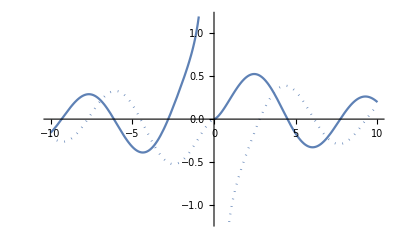

```mathematica
ReImPlot[HankelH1[3/2,x],{x,-10,10}]
```

```mathematica
?HankelH2
```

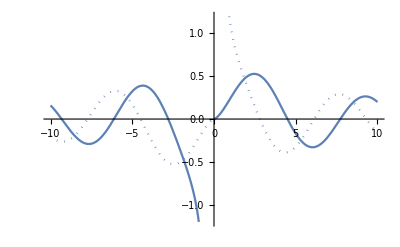

```mathematica
ReImPlot[HankelH2[3/2,x],{x,-10,10}]
```

## H Counter term Equation 28

```mathematica
Clear[Hterm1]
Hterm1 = 
TensorValues[MergeTensors[CovariantD[tensorList[[5]],-μ,-ν]]]// Expand // Simplify // Expand // Apart // Expand  ;
Hterm1 // MatrixForm
```

((90 a'[η]^2 a''[η])/a[η]^5-(18 a''[η]^2)/a[η]^4-(42 a'[η] a^(3)[η])/a[η]^4+(6 a^(4)[η])/a[η]^3 | 0 | 0 | 0
0 | (18 a'[η]^2 a''[η])/a[η]^5-(6 a'[η] a^(3)[η])/a[η]^4 | 0 | 0
0 | 0 | (18 a'[η]^2 a''[η])/a[η]^5-(6 a'[η] a^(3)[η])/a[η]^4 | 0
0 | 0 | 0 | (18 a'[η]^2 a''[η])/a[η]^5-(6 a'[η] a^(3)[η])/a[η]^4)

```mathematica
Clear[Hterm2]
Hterm2 = 
TensorValues[MergeTensors[tensorList[[1]][-μ,-ν]CovariantD[tensorList[[5]],-ρ,ρ]]] // Expand // Simplify // Expand // Apart // Expand  ;
Hterm2 // MatrixForm
```

((36 a'[η]^2 a''[η])/a[η]^5-(18 a''[η]^2)/a[η]^4-(24 a'[η] a^(3)[η])/a[η]^4+(6 a^(4)[η])/a[η]^3 | 0 | 0 | 0
0 | -(36 a'[η]^2 a''[η])/a[η]^5+(18 a''[η]^2)/a[η]^4+(24 a'[η] a^(3)[η])/a[η]^4-(6 a^(4)[η])/a[η]^3 | 0 | 0
0 | 0 | -(36 a'[η]^2 a''[η])/a[η]^5+(18 a''[η]^2)/a[η]^4+(24 a'[η] a^(3)[η])/a[η]^4-(6 a^(4)[η])/a[η]^3 | 0
0 | 0 | 0 | -(36 a'[η]^2 a''[η])/a[η]^5+(18 a''[η]^2)/a[η]^4+(24 a'[η] a^(3)[η])/a[η]^4-(6 a^(4)[η])/a[η]^3)

```mathematica
Clear[Hterm3]
Hterm3 = 
TensorValues[MergeTensors[MultiplyTensorScalar[ tensorList[[1]][-μ,-ν],( TensorValues[tensorList[[5]]] )^2]]] ;
Hterm3 // MatrixForm
```

(-(36 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | (36 a''[η]^2)/a[η]^4 | 0 | 0
0 | 0 | (36 a''[η]^2)/a[η]^4 | 0
0 | 0 | 0 | (36 a''[η]^2)/a[η]^4)

```mathematica
Clear[Hterm4]
Hterm4 = 
TensorValues[MergeTensors[MultiplyTensorScalar[( TensorValues[tensorList[[5]]] )^2 ,tensorList[[1]][-μ,-ν]]]] ;
Hterm4 // MatrixForm
```

(-(36 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | (36 a''[η]^2)/a[η]^4 | 0 | 0
0 | 0 | (36 a''[η]^2)/a[η]^4 | 0
0 | 0 | 0 | (36 a''[η]^2)/a[η]^4)

```mathematica
Clear[H] (* Use these components for ToTensor *) 
H = 
-2 Hterm1 + 2 Hterm2 - (1/2) Hterm3 + 2 Hterm4 // Expand // Simplify // Expand // Apart // Expand ;
H // MatrixForm
```

(-(108 a'[η]^2 a''[η])/a[η]^5-(54 a''[η]^2)/a[η]^4+(36 a'[η] a^(3)[η])/a[η]^4 | 0 | 0 | 0
0 | -(108 a'[η]^2 a''[η])/a[η]^5+(90 a''[η]^2)/a[η]^4+(60 a'[η] a^(3)[η])/a[η]^4-(12 a^(4)[η])/a[η]^3 | 0 | 0
0 | 0 | -(108 a'[η]^2 a''[η])/a[η]^5+(90 a''[η]^2)/a[η]^4+(60 a'[η] a^(3)[η])/a[η]^4-(12 a^(4)[η])/a[η]^3 | 0
0 | 0 | 0 | -(108 a'[η]^2 a''[η])/a[η]^5+(90 a''[η]^2)/a[η]^4+(60 a'[η] a^(3)[η])/a[η]^4-(12 a^(4)[η])/a[η]^3)

## A Counter term Equation 29

```mathematica
Clear[Aterm1]
Aterm1 = 
TensorValues[MergeTensors[CovariantD[MergeTensors[CovariantD[ tensorList[[8]][-μ,α,-ν,β] , -α]],-β]]  ] ;
Aterm1 // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[Aterm2]
Aterm2 = 
TensorValues[MergeTensors[tensorList[[4]][-α,-β] tensorList[[8]][-μ,α,-ν,β]]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[A] (* Use these components for ToTensor *) 
A = 
-4 Aterm1 -2 Aterm2  ;
A // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## B Counter term Equation 30 (This gives trace anomaly)

```mathematica
Clear[Bterm1]
Bterm1 = 
TensorValues[MergeTensors[tensorList[[8]][-α,-μ,-β,-ν] tensorList[[4]][α,β]]] ;
Bterm1 // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[Bterm2]
Bterm2 = 
TensorValues[MergeTensors[tensorList[[1]][-μ,-ν] tensorList[[4]][-α,-β] tensorList[[4]][α,β]] ]// Expand // Simplify // Expand // Apart // Expand  ;
Bterm2  // MatrixForm
```

(-(12 a'[η]^4)/a[η]^6+(12 a'[η]^2 a''[η])/a[η]^5-(12 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | (12 a'[η]^4)/a[η]^6-(12 a'[η]^2 a''[η])/a[η]^5+(12 a''[η]^2)/a[η]^4 | 0 | 0
0 | 0 | (12 a'[η]^4)/a[η]^6-(12 a'[η]^2 a''[η])/a[η]^5+(12 a''[η]^2)/a[η]^4 | 0
0 | 0 | 0 | (12 a'[η]^4)/a[η]^6-(12 a'[η]^2 a''[η])/a[η]^5+(12 a''[η]^2)/a[η]^4)

```mathematica
(* Not working figure out why *) 
Clear[Bterm3]
Bterm3 = 
TensorValues[MergeTensors[MultiplyTensorScalar[( TensorValues[tensorList[[5]]] )^2 ,tensorList[[1]][-μ,-ν]]]] ;
Bterm3 // MatrixForm
```

(-(36 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | (36 a''[η]^2)/a[η]^4 | 0 | 0
0 | 0 | (36 a''[η]^2)/a[η]^4 | 0
0 | 0 | 0 | (36 a''[η]^2)/a[η]^4)

```mathematica
Clear[Bterm4]
Bterm4 = 
TensorValues[MergeTensors[tensorList[[4]][-μ,α] tensorList[[4]][-ν,-α]] ]// Expand // Simplify // Expand // Apart // Expand  ;
Bterm4  // MatrixForm
```

(-(9 a'[η]^4)/a[η]^6+(18 a'[η]^2 a''[η])/a[η]^5-(9 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | a'[η]^4/a[η]^6+(2 a'[η]^2 a''[η])/a[η]^5+a''[η]^2/a[η]^4 | 0 | 0
0 | 0 | a'[η]^4/a[η]^6+(2 a'[η]^2 a''[η])/a[η]^5+a''[η]^2/a[η]^4 | 0
0 | 0 | 0 | a'[η]^4/a[η]^6+(2 a'[η]^2 a''[η])/a[η]^5+a''[η]^2/a[η]^4)

```mathematica
Clear[Bterm5]
Bterm5 = 
TensorValues[MergeTensors[MultiplyTensorScalar[ tensorList[[1]][-μ,-ν] , ( TensorValues[tensorList[[5]]] )^2 ] ]] ;
Bterm5 // MatrixForm
```

(-(36 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | (36 a''[η]^2)/a[η]^4 | 0 | 0
0 | 0 | (36 a''[η]^2)/a[η]^4 | 0
0 | 0 | 0 | (36 a''[η]^2)/a[η]^4)

```mathematica
Clear[B] (* Use these components for ToTensor *) 
B = 
-2 Bterm1 + (1/2) Bterm2 +(2/3) Bterm3- Bterm4 - (1/4) Bterm5 // Expand // Simplify // Expand // Apart // Expand   ;
B // MatrixForm
```

((3 a'[η]^4)/a[η]^6-(12 a'[η]^2 a''[η])/a[η]^5-(12 a''[η]^2)/a[η]^4 | 0 | 0 | 0
0 | (5 a'[η]^4)/a[η]^6-(8 a'[η]^2 a''[η])/a[η]^5+(20 a''[η]^2)/a[η]^4 | 0 | 0
0 | 0 | (5 a'[η]^4)/a[η]^6-(8 a'[η]^2 a''[η])/a[η]^5+(20 a''[η]^2)/a[η]^4 | 0
0 | 0 | 0 | (5 a'[η]^4)/a[η]^6-(8 a'[η]^2 a''[η])/a[η]^5+(20 a''[η]^2)/a[η]^4)

```mathematica
Clear[eq60]
eq60[g_] := 
π k^4(1+k^2 ηr^2) (H^4/(2 π k)^6)Integrate[ g^4 , {η,-∞,ηr}]
```

```mathematica
Clear[eq111]
eq111[g_]:= 
Integrate[ g ( g^3 - 4 η^2 ( D[g,η] )^2) , {η,-∞,0}]
```

```mathematica
Clear[eq113]
eq113 = 
Assuming[Re[p]>0 , eq111[ Exp[p η] ] ]
```

-5/(108 p)

```mathematica
(* 
This one seems to take forever, so..... redo this? 

Assuming[Re[p]>0 , eq111[ Exp[-(Abs[p η])^b ] ]]
*)
```

$Aborted

```mathematica
Clear[eq117]
eq117 = 
eq111[ 1/(1+ (η/Abs[η0])^2)]
```

-1/32 π Abs[η0]